# Omicron US analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"Arizona","Kentucky","Nevada","North Carolina"};
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-11-01

```mathematica
startDate="2021-11-01";
```

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-03-02

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-03-02

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
states=Union[rtData[[All,2]]]
```

{Arizona,Arkansas,California,Colorado,Connecticut,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Missouri,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Rhode Island,South Carolina,Tennessee,Texas,Utah,Virginia,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Arkansas,California,Colorado,Connecticut,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Missouri,Nebraska,New Jersey,New Mexico,New York,North Dakota,Ohio,Oregon,Pennsylvania,Rhode Island,South Carolina,Tennessee,Texas,Utah,Virginia,Wisconsin}

```mathematica
Length[states]
```

31

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.001];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,4.1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,4.1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

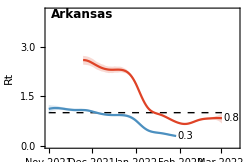
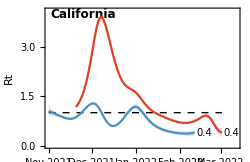
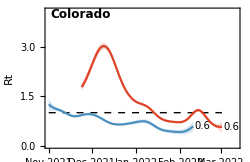
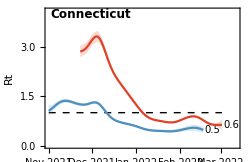
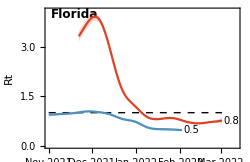
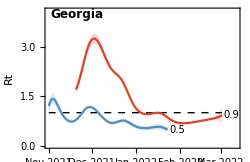
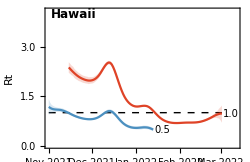
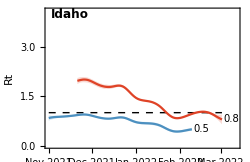
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arkansas→{2022-03-02,0.8,0.7,1.},California→{2022-03-02,0.4,0.2,0.5},Colorado→{2022-03-02,0.6,0.4,0.7},Connecticut→{2022-03-02,0.6,0.5,0.8},Florida→{2022-03-02,0.8,0.7,0.9},Georgia→{2022-03-02,0.9,0.7,1.2},Hawaii→{2022-03-02,1.,0.7,1.2},Idaho→{2022-03-02,0.8,0.6,0.9},Illinois→{2022-03-02,0.7,0.6,0.9},Indiana→{2022-03-02,0.7,0.6,0.9},Louisiana→{2022-03-02,1.4,1.,1.7},Maryland→{2022-03-02,0.8,0.7,1.},Massachusetts→{2022-03-02,0.6,0.5,0.8},Michigan→{2022-03-02,0.4,0.3,0.6},Minnesota→{2022-03-02,0.6,0.5,0.7},Missouri→{2022-03-02,0.7,0.6,0.9},Nebraska→{2022-03-02,0.9,0.7,1.1},New Jersey→{2022-03-02,0.9,0.7,1.1},New Mexico→{2022-03-02,1.2,0.9,1.5},New York→{2022-03-02,0.9,0.8,1.},North Dakota→{2022-03-02,0.8,0.6,0.9},Ohio→{2022-03-02,0.9,0.7,1.},Oregon→{2022-03-02,0.7,0.6,0.8},Pennsylvania→{2022-03-02,0.7,0.6,0.8},Rhode Island→{2022-03-02,1.1,0.8,1.3},South Carolina→{2022-03-02,0.6,0.5,0.7},Tennessee→{2022-03-02,0.8,0.6,0.9},Texas→{2022-03-02,0.8,0.6,1.},Utah→{2022-03-02,0.6,0.4,0.7},Virginia→{2022-03-02,0.9,0.7,1.},Wisconsin→{2022-03-02,0.9,0.7,1.1}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.001];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,15]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

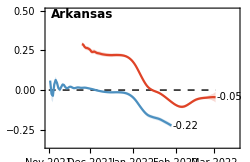
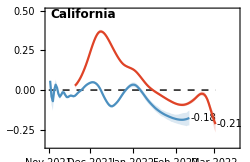
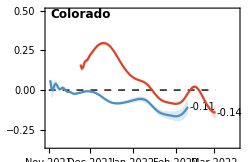
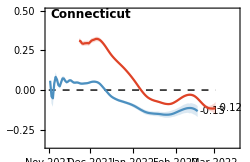
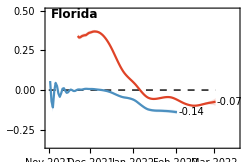
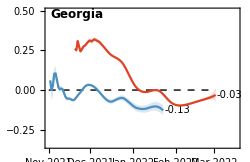
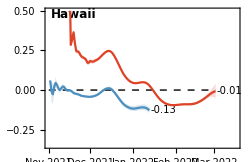
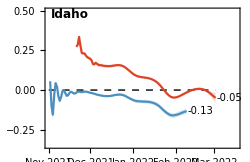
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Arkansas→{2022-03-02,-0.05,-0.08,-0.01},California→{2022-03-02,-0.21,-0.27,-0.15},Colorado→{2022-03-02,-0.14,-0.19,-0.09},Connecticut→{2022-03-02,-0.12,-0.16,-0.07},Florida→{2022-03-02,-0.07,-0.1,-0.05},Georgia→{2022-03-02,-0.03,-0.07,0.},Hawaii→{2022-03-02,-0.01,-0.05,0.04},Idaho→{2022-03-02,-0.05,-0.08,-0.02},Illinois→{2022-03-02,-0.08,-0.12,-0.05},Indiana→{2022-03-02,-0.08,-0.11,-0.04},Louisiana→{2022-03-02,0.07,0.02,0.12},Maryland→{2022-03-02,-0.04,-0.08,-0.01},Massachusetts→{2022-03-02,-0.11,-0.14,-0.07},Michigan→{2022-03-02,-0.19,-0.23,-0.14},Minnesota→{2022-03-02,-0.12,-0.15,-0.09},Missouri→{2022-03-02,-0.08,-0.12,-0.04},Nebraska→{2022-03-02,-0.04,-0.08,0.01},New Jersey→{2022-03-02,-0.02,-0.06,0.02},New Mexico→{2022-03-02,0.03,-0.01,0.09},New York→{2022-03-02,-0.04,-0.06,-0.01},North Dakota→{2022-03-02,-0.07,-0.1,-0.04},Ohio→{2022-03-02,-0.03,-0.06,0.},Oregon→{2022-03-02,-0.08,-0.11,-0.06},Pennsylvania→{2022-03-02,-0.07,-0.1,-0.05},Rhode Island→{2022-03-02,0.03,-0.01,0.07},South Carolina→{2022-03-02,-0.12,-0.15,-0.09},Tennessee→{2022-03-02,-0.06,-0.09,-0.03},Texas→{2022-03-02,-0.06,-0.11,-0.02},Utah→{2022-03-02,-0.14,-0.19,-0.09},Virginia→{2022-03-02,-0.04,-0.06,-0.02},Wisconsin→{2022-03-02,-0.04,-0.07,0.}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arkansas→{2022-03-02,-15.3,-55.5,-8.9},California→{2022-03-02,-3.2,-4.7,-2.6},Colorado→{2022-03-02,-4.9,-7.5,-3.7},Connecticut→{2022-03-02,-6.,-9.3,-4.5},Florida→{2022-03-02,-9.5,-13.6,-7.1},Georgia→{2022-03-02,-22.8,350.1,-9.3},Hawaii→{2022-03-02,-97.1,17.2,-13.5},Idaho→{2022-03-02,-14.,-36.8,-8.2},Illinois→{2022-03-02,-8.6,-14.7,-5.9},Indiana→{2022-03-02,-9.,-15.9,-6.4},Louisiana→{2022-03-02,10.5,6.,36.3},Maryland→{2022-03-02,-15.5,-53.2,-8.9},Massachusetts→{2022-03-02,-6.5,-10.2,-4.8},Michigan→{2022-03-02,-3.6,-5.,-3.},Minnesota→{2022-03-02,-5.7,-8.,-4.5},Missouri→{2022-03-02,-8.9,-16.1,-6.},Nebraska→{2022-03-02,-19.8,117.6,-8.8},New Jersey→{2022-03-02,-32.1,46.,-12.2},New Mexico→{2022-03-02,23.1,8.1,-58.2},New York→{2022-03-02,-19.2,-51.6,-11.3},North Dakota→{2022-03-02,-9.8,-16.9,-6.8},Ohio→{2022-03-02,-21.,-3396.3,-11.1},Oregon→{2022-03-02,-8.4,-12.4,-6.4},Pennsylvania→{2022-03-02,-9.4,-13.4,-6.9},Rhode Island→{2022-03-02,25.,10.1,-86.2},South Carolina→{2022-03-02,-5.9,-7.7,-4.7},Tennessee→{2022-03-02,-10.8,-20.7,-7.6},Texas→{2022-03-02,-11.7,-42.,-6.6},Utah→{2022-03-02,-4.9,-7.9,-3.7},Virginia→{2022-03-02,-16.7,-38.6,-11.},Wisconsin→{2022-03-02,-17.6,-296.2,-10.}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{20,240000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

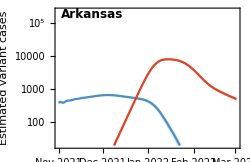
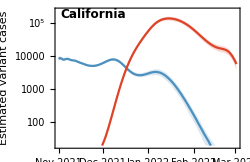
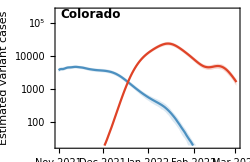
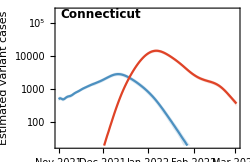
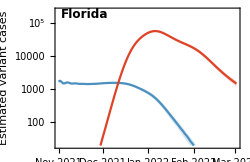
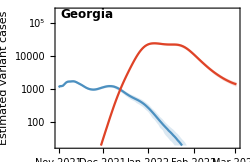
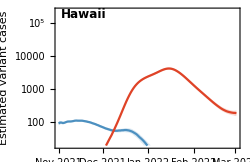
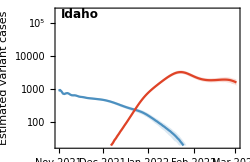
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

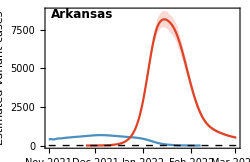
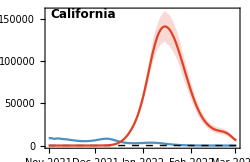
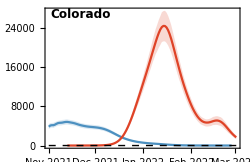
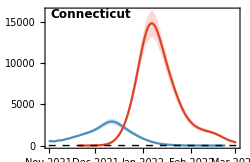
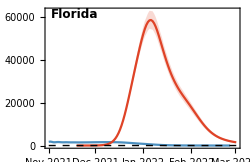
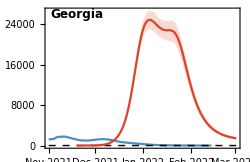
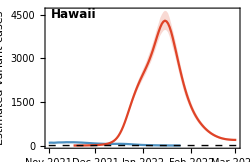
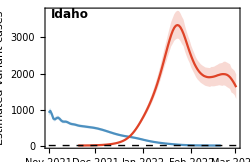
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,states]
```

{Arkansas→{2022-03-02,510,433,579},California→{2022-03-02,5874,3941,7374},Colorado→{2022-03-02,1673,1283,2065},Connecticut→{2022-03-02,373,306,439},Florida→{2022-03-02,1495,1202,1792},Georgia→{2022-03-02,1432,1195,1669},Hawaii→{2022-03-02,192,156,235},Idaho→{2022-03-02,1621,1293,1974},Illinois→{2022-03-02,2196,1774,2569},Indiana→{2022-03-02,631,529,744},Louisiana→{2022-03-02,984,762,1156},Maryland→{2022-03-02,485,400,563},Massachusetts→{2022-03-02,1265,978,1570},Michigan→{2022-03-02,1517,1158,1912},Minnesota→{2022-03-02,964,776,1155},Missouri→{2022-03-02,832,507,1128},Nebraska→{2022-03-02,150,108,186},New Jersey→{2022-03-02,1413,1156,1650},New Mexico→{2022-03-02,535,436,639},New York→{2022-03-02,1369,1136,1623},North Dakota→{2022-03-02,128,100,154},Ohio→{2022-03-02,796,639,936},Oregon→{2022-03-02,727,605,854},Pennsylvania→{2022-03-02,1087,911,1244},Rhode Island→{2022-03-02,223,185,256},South Carolina→{2022-03-02,452,376,513},Tennessee→{2022-03-02,1345,1046,1631},Texas→{2022-03-02,3521,2512,4500},Utah→{2022-03-02,479,301,654},Virginia→{2022-03-02,1662,1427,1903},Wisconsin→{2022-03-02,695,557,849}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated Omicron frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=variantCountryFrequencyPlot[country,variants[[3]],colors[[3]]]
```

```mathematica
panels=Map[countryFrequencyPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

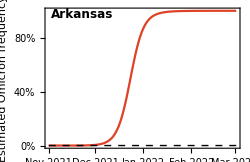
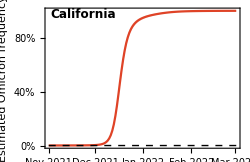
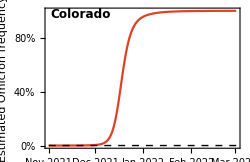
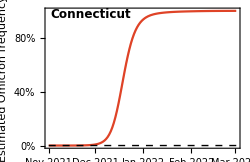
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron"][[-1,1]],Round[fGather[#,"Omicron"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Arkansas→{2022-03-02,1.,1.,1.},California→{2022-03-02,1.,1.,1.},Colorado→{2022-03-02,1.,1.,1.},Connecticut→{2022-03-02,1.,1.,1.},Florida→{2022-03-02,1.,1.,1.},Georgia→{2022-03-02,1.,1.,1.},Hawaii→{2022-03-02,1.,1.,1.},Idaho→{2022-03-02,1.,1.,1.},Illinois→{2022-03-02,1.,1.,1.},Indiana→{2022-03-02,1.,1.,1.},Louisiana→{2022-03-02,1.,1.,1.},Maryland→{2022-03-02,1.,1.,1.},Massachusetts→{2022-03-02,1.,1.,1.},Michigan→{2022-03-02,1.,1.,1.},Minnesota→{2022-03-02,1.,1.,1.},Missouri→{2022-03-02,1.,1.,1.},Nebraska→{2022-03-02,0.98,0.96,0.99},New Jersey→{2022-03-02,1.,1.,1.},New Mexico→{2022-03-02,1.,1.,1.},New York→{2022-03-02,1.,1.,1.},North Dakota→{2022-03-02,1.,1.,1.},Ohio→{2022-03-02,1.,1.,1.},Oregon→{2022-03-02,1.,1.,1.},Pennsylvania→{2022-03-02,1.,1.,1.},Rhode Island→{2022-03-02,1.,1.,1.},South Carolina→{2022-03-02,1.,1.,1.},Tennessee→{2022-03-02,1.,1.,1.},Texas→{2022-03-02,1.,1.,1.},Utah→{2022-03-02,1.,1.,1.},Virginia→{2022-03-02,1.,1.,1.},Wisconsin→{2022-03-02,1.,1.,1.}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[state_,variant_]:=Module[{popSize,stateName},
stateName=StringReplace[state," "->""];
popSize=QuantityMagnitude[AdministrativeDivisionData[{stateName, "UnitedStates"},"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[state,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron},
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,650},
{-0.25,0.45}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,states];
```

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt.png

```mathematica
stateLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,states];
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]],Opacity[0.5]],Prolog->{Dashed,Black,Line[{{0,0},{1000,0}}]}];
```

```mathematica
statePoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,states];
```

```mathematica
figPoints=ListLogLinearPlot[statePoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,150},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt-overlay.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt-overlay.png

### Growth rate vs peak incidence

```mathematica
initialR[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,(#1[[1]]-10)^2<(#2[[1]]-10)^2&];
sorted[[1,2]]
]
```

```mathematica
initialR["Washington","Omicron"]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1,2⟧

```mathematica
peakIncidence[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,#1[[1]]>#2[[1]]&];
sorted[[1,1]]
]
```

```mathematica
peakIncidence["Washington","Omicron"]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

```mathematica
pairs=Map[{initialR[#,"Omicron"],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Initial epidemic growth rate r","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
rValues=Map[initialR[#,"Omicron"]&,states]
```

{0.220999,0.273211,0.286362,-0.115472,-0.081367,0.250199,0.243273,0.157187,0.242795,-0.0766008,0.158109,-0.0199099,0.295942,0.232114,0.173971,0.203918,-0.0696995,0.255692,0.173451,-0.054184,0.162233,0.202868,0.202571,0.191945,0.211545,-0.113878,0.18628,0.182469,0.237576,0.242475,0.224324}

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.15],0.0],Lighter[ColorData["Rainbow"][0.3],0.0],Lighter[ColorData["Rainbow"][0.7],0.0],Lighter[ColorData["Rainbow"][0.9],0.0]},t]
```

```mathematica
standardizedColorFunction[t_,min_,max_]:=baseColorFunction[(t-min)/(max-min)]
```

```mathematica
phaseColors=Map[standardizedColorFunction[#,Min[rValues],Max[rValues]]&,rValues]
```

{RGBColor[0.8467153161100476, 0.565310547426809, 0.2212475896390611],RGBColor[0.8789297088545962, 0.442937887178856, 0.19209339858931282],RGBColor[0.887043877157483, 0.4121146347029296, 0.18475003455982308],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.26047623083952287, 0.350870258993033, 0.7790499361287977],RGBColor[0.8647318254576464, 0.49687131919951716, 0.20494255605563724],RGBColor[0.8604583529136609, 0.5131049389933462, 0.20881007067809707],RGBColor[0.8023229274867767, 0.7093672956742858, 0.2618281696885091],RGBColor[0.8601635602470438, 0.5142247664916199, 0.20907685955693062],RGBColor[0.2622101850540799, 0.3608124241219689, 0.7778096626336538],RGBColor[0.8057559448726838, 0.7103445549494174, 0.25849012458939624],RGBColor[0.2828343599745745, 0.47906753777270894, 0.763057475235421],RGBColor[0.8929546, 0.38966160000000005, 0.17940080000000003],RGBColor[0.8535736709849026, 0.5392577474371976, 0.21504074321814481],RGBColor[0.8176999534860337, 0.675531067196205, 0.24750664198333897],RGBColor[0.8361766032193872, 0.6053439058776753, 0.23078517898520048],RGBColor[0.264720866628678, 0.37520819685418527, 0.7760138067883392],RGBColor[0.8681210619099685, 0.48399664283455046, 0.20187527964203816],RGBColor[0.817378833765513, 0.676750903148719, 0.2477972569813041],RGBColor[0.2703654334320434, 0.4075730740633029, 0.7719763261334237],RGBColor[0.8104575148444698, 0.703042884360622, 0.2540610861877222],RGBColor[0.8355286195816775, 0.6078053982352216, 0.23137160750864677],RGBColor[0.8353457677960003, 0.6084999964423594, 0.23153708931473546],RGBColor[0.8287895663037942, 0.6334050078167748, 0.23747048537096777],RGBColor[0.8408825563922375, 0.5874674239793339, 0.22652626717021174],RGBColor[0.24864889587104153, 0.2830545598790152, 0.7875098654374522],RGBColor[0.8252945588917655, 0.6466814758224813, 0.24063348504687543],RGBColor[0.8229428317143901, 0.6556149706474468, 0.24276181023275648],RGBColor[0.8569433426169931, 0.5264573918616368, 0.2119911730674391],RGBColor[0.8599658574609576, 0.5149757791232611, 0.2092557815947394],RGBColor[0.8487673887228737, 0.5575153489686293, 0.2193904533746374]}

```mathematica
Min[rValues]
```

-0.115472

```mathematica
Max[rValues]
```

0.295942

```mathematica
legend=PointLegend[Table[standardizedColorFunction[i,Min[rValues],Max[rValues]],{i,0.15,0.3,0.05}],Table["initial r = "<>ToString[NumberForm[Round[i,0.01],{3,2}]],{i,0.15,0.3,0.05}],LegendMarkerSize->20,LegendLayout->{"Column",1},Spacings->{0,1}]
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{3,600},
{-0.25,0.4}},PlotStyle->Map[Directive[#,Opacity[0.5]]&,phaseColors],PlotLegends->Placed[legend,Right]]
```

-Graphics-

```mathematica
figPoints=ListLogLinearPlot[Map[{#}&,statePoints],Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->phaseColors,PlotMarkers->{"•",Scaled[0.1]}]
```

-Graphics-

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

### Mapping

```mathematica
mapFig=Module[{entities},
GeoGraphics[{Map[{GeoStyling[Opacity@1,EdgeForm[GrayLevel[0.8]],FaceForm[GrayLevel[0.9]]],Polygon@#}&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]]},GeoRangePadding->None,GeoRange->{{25,49},{-125,-67}},GeoBackground->None,ImageSize->400,ImageMargins->0]
]
```

-Graphics-

```mathematica
fullStateNamesToAbbreviations={"Alaska"->"AK","Washington"->"WA","Idaho"->"ID","Montana"->"MT","Oregon"->"OR","Nevada"->"NV","Wyoming"->"WY","California"->"CA","Utah"->"UT","Colorado"->"CO","Hawaii"->"HI","Arizona"->"AZ","New Mexico"->"NM","Oklahoma"->"OK","Texas"->"TX","North Dakota"->"ND","Minnesota"->"MN","Illinois"->"IL","Wisconsin"->"WI","Michigan"->"MI","South Dakota"->"SD","Iowa"->"IA","Indiana"->"IN","Ohio"->"OH","Nebraska"->"NE","Missouri"->"MO","Kansas"->"KS","Kentucky"->"KY","West Virginia"->"WV","Virginia"->"VA","Arkansas"->"AR","Tennessee"->"TN","North Carolina"->"NC","South Carolina"->"SC","Louisiana"->"LA","Mississippi"->"MS","Alabama"->"AL","Georgia"-> "GA","Florida"->"FL","Maine"->"ME","Vermont"->"VT","New Hampshire"->"NH","New York"->"NY","Massachusetts"->"MA","Rhode Island"->"RI","Pennsylvania"->"PA","New Jersey"->"NJ","Connecticut"-> "CT","Maryland"->"MD","Washington DC"->"DC","Delaware"->"DE"};
```

```mathematica
abbreviationsToFullStateNames=Map[#[[2]]->#[[1]]&,fullStateNamesToAbbreviations];
```

```mathematica
geoCasesPerCapita=DeleteCases[Map[#->With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],peakIncidence[state,"Omicron"],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x[[2]]==Null]
```

{Arkansas, United States→271.389,California, United States→355.87,Colorado, United States→421.848,Connecticut, United States→410.221,Florida, United States→270.809,Georgia, United States→232.097,Idaho, United States→181.658,Illinois, United States→306.791,Indiana, United States→265.998,Louisiana, United States→347.251,Maryland, United States→213.507,Massachusetts, United States→500.109,Michigan, United States→293.055,Minnesota, United States→375.41,Missouri, United States→194.991,Nebraska, United States→347.776,New Jersey, United States→368.057,New Mexico, United States→419.673,New York, United States→306.598,North Dakota, United States→324.996,Ohio, United States→199.24,Oregon, United States→269.103,Pennsylvania, United States→223.727,Rhode Island, United States→448.112,South Carolina, United States→323.121,Tennessee, United States→291.113,Texas, United States→228.117,Utah, United States→676.345,Virginia, United States→272.181,Wisconsin, United States→407.547}

```mathematica
geoColors=DeleteCases[Map[With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],standardizedColorFunction[initialR[state,"Omicron"],Min[rValues],Max[rValues]],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x==Null]
```

{RGBColor[0.8467153161100476, 0.565310547426809, 0.2212475896390611],RGBColor[0.8789297088545962, 0.442937887178856, 0.19209339858931282],RGBColor[0.887043877157483, 0.4121146347029296, 0.18475003455982308],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.26047623083952287, 0.350870258993033, 0.7790499361287977],RGBColor[0.8647318254576464, 0.49687131919951716, 0.20494255605563724],RGBColor[0.8023229274867767, 0.7093672956742858, 0.2618281696885091],RGBColor[0.8601635602470438, 0.5142247664916199, 0.20907685955693062],RGBColor[0.2622101850540799, 0.3608124241219689, 0.7778096626336538],RGBColor[0.8057559448726838, 0.7103445549494174, 0.25849012458939624],RGBColor[0.2828343599745745, 0.47906753777270894, 0.763057475235421],RGBColor[0.8929546, 0.38966160000000005, 0.17940080000000003],RGBColor[0.8535736709849026, 0.5392577474371976, 0.21504074321814481],RGBColor[0.8176999534860337, 0.675531067196205, 0.24750664198333897],RGBColor[0.8361766032193872, 0.6053439058776753, 0.23078517898520048],RGBColor[0.264720866628678, 0.37520819685418527, 0.7760138067883392],RGBColor[0.8681210619099685, 0.48399664283455046, 0.20187527964203816],RGBColor[0.817378833765513, 0.676750903148719, 0.2477972569813041],RGBColor[0.2703654334320434, 0.4075730740633029, 0.7719763261334237],RGBColor[0.8104575148444698, 0.703042884360622, 0.2540610861877222],RGBColor[0.8355286195816775, 0.6078053982352216, 0.23137160750864677],RGBColor[0.8353457677960003, 0.6084999964423594, 0.23153708931473546],RGBColor[0.8287895663037942, 0.6334050078167748, 0.23747048537096777],RGBColor[0.8408825563922375, 0.5874674239793339, 0.22652626717021174],RGBColor[0.24864889587104153, 0.2830545598790152, 0.7875098654374522],RGBColor[0.8252945588917655, 0.6466814758224813, 0.24063348504687543],RGBColor[0.8229428317143901, 0.6556149706474468, 0.24276181023275648],RGBColor[0.8569433426169931, 0.5264573918616368, 0.2119911730674391],RGBColor[0.8599658574609576, 0.5149757791232611, 0.2092557815947394],RGBColor[0.8487673887228737, 0.5575153489686293, 0.2193904533746374]}

```mathematica
bubbleFig=GeoBubbleChart[geoCasesPerCapita,ChartStyle->geoColors,GeoRange->{{25,50},{-125,-67}},BubbleSizes->Medium,ColorFunctionScaling->True]
```

-Graphics-

```mathematica
fig=Show[mapFig,bubbleFig]
```

-Graphics-

### Parallel epidemics

```mathematica
translatedSeries[country_,variant_]:=Module[{series,sorted,initialDate},
series=perCapitaPGather[country,variant];
sorted=Sort[series,(#1[[2]]-10)^2<(#2[[2]]-10)^2&];
initialDate=sorted[[1,1]];
Map[{QuantityMagnitude[DateDifference[initialDate,#[[1]]]],#[[2]]}&,series]
]
```

```mathematica
translatedSeries["Washington","Omicron"]
```

Part::partw: Part 1 of {} does not exist.

{}

```mathematica
tSeries=Map[translatedSeries[#,"Omicron"]&,states];
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListLogPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{4,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,50,100,200,500,1000},Automatic},{Automatic,Automatic}}]
]
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{0,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}]
]
```

```mathematica
panels=MapThread[variantCountryTranslatedPrevalencePlot[#1,"Omicron",#2]&,{states,phaseColors}];
```

```mathematica
fig=Show[panels]
```

-Graphics-

## Vaccination data

Download at https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD

### Import data

```mathematica
vacData=Import["https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD"];
```

```mathematica
vacHeader=vacData[[1]]
```

{Date,MMWR_week,Location,Distributed,Distributed_Janssen,Distributed_Moderna,Distributed_Pfizer,Distributed_Unk_Manuf,Dist_Per_100K,Distributed_Per_100k_12Plus,Distributed_Per_100k_18Plus,Distributed_Per_100k_65Plus,Administered,Administered_12Plus,Administered_18Plus,Administered_65Plus,Administered_Janssen,Administered_Moderna,Administered_Pfizer,Administered_Unk_Manuf,Admin_Per_100K,Admin_Per_100k_12Plus,Admin_Per_100k_18Plus,Admin_Per_100k_65Plus,Recip_Administered,Administered_Dose1_Recip,Administered_Dose1_Pop_Pct,Administered_Dose1_Recip_12Plus,Administered_Dose1_Recip_12PlusPop_Pct,Administered_Dose1_Recip_18Plus,Administered_Dose1_Recip_18PlusPop_Pct,Administered_Dose1_Recip_65Plus,Administered_Dose1_Recip_65PlusPop_Pct,Series_Complete_Yes,Series_Complete_Pop_Pct,Series_Complete_12Plus,Series_Complete_12PlusPop_Pct,Series_Complete_18Plus,Series_Complete_18PlusPop_Pct,Series_Complete_65Plus,Series_Complete_65PlusPop_Pct,Series_Complete_Janssen,Series_Complete_Moderna,Series_Complete_Pfizer,Series_Complete_Unk_Manuf,Series_Complete_Janssen_12Plus,Series_Complete_Moderna_12Plus,Series_Complete_Pfizer_12Plus,Series_Complete_Unk_Manuf_12Plus,Series_Complete_Janssen_18Plus,Series_Complete_Moderna_18Plus,Series_Complete_Pfizer_18Plus,Series_Complete_Unk_Manuf_18Plus,Series_Complete_Janssen_65Plus,Series_Complete_Moderna_65Plus,Series_Complete_Pfizer_65Plus,Series_Complete_Unk_Manuf_65Plus,Additional_Doses,Additional_Doses_Vax_Pct,Additional_Doses_12Plus,Additional_Doses_12Plus_Vax_Pct,Additional_Doses_18Plus,Additional_Doses_18Plus_Vax_Pct,Additional_Doses_50Plus,Additional_Doses_50Plus_Vax_Pct,Additional_Doses_65Plus,Additional_Doses_65Plus_Vax_Pct,Additional_Doses_Moderna,Additional_Doses_Pfizer,Additional_Doses_Janssen,Additional_Doses_Unk_Manuf,Administered_Dose1_Recip_5Plus,Administered_Dose1_Recip_5PlusPop_Pct,Series_Complete_5Plus,Series_Complete_5PlusPop_Pct,Administered_5Plus,Admin_Per_100k_5Plus,Distributed_Per_100k_5Plus,Series_Complete_Moderna_5Plus,Series_Complete_Pfizer_5Plus,Series_Complete_Janssen_5Plus,Series_Complete_Unk_Manuf_5Plus}

```mathematica
vacHeaderRules=MapIndexed[#1->#2[[1]]&,vacHeader]
```

{Date→1,MMWR_week→2,Location→3,Distributed→4,Distributed_Janssen→5,Distributed_Moderna→6,Distributed_Pfizer→7,Distributed_Unk_Manuf→8,Dist_Per_100K→9,Distributed_Per_100k_12Plus→10,Distributed_Per_100k_18Plus→11,Distributed_Per_100k_65Plus→12,Administered→13,Administered_12Plus→14,Administered_18Plus→15,Administered_65Plus→16,Administered_Janssen→17,Administered_Moderna→18,Administered_Pfizer→19,Administered_Unk_Manuf→20,Admin_Per_100K→21,Admin_Per_100k_12Plus→22,Admin_Per_100k_18Plus→23,Admin_Per_100k_65Plus→24,Recip_Administered→25,Administered_Dose1_Recip→26,Administered_Dose1_Pop_Pct→27,Administered_Dose1_Recip_12Plus→28,Administered_Dose1_Recip_12PlusPop_Pct→29,Administered_Dose1_Recip_18Plus→30,Administered_Dose1_Recip_18PlusPop_Pct→31,Administered_Dose1_Recip_65Plus→32,Administered_Dose1_Recip_65PlusPop_Pct→33,Series_Complete_Yes→34,Series_Complete_Pop_Pct→35,Series_Complete_12Plus→36,Series_Complete_12PlusPop_Pct→37,Series_Complete_18Plus→38,Series_Complete_18PlusPop_Pct→39,Series_Complete_65Plus→40,Series_Complete_65PlusPop_Pct→41,Series_Complete_Janssen→42,Series_Complete_Moderna→43,Series_Complete_Pfizer→44,Series_Complete_Unk_Manuf→45,Series_Complete_Janssen_12Plus→46,Series_Complete_Moderna_12Plus→47,Series_Complete_Pfizer_12Plus→48,Series_Complete_Unk_Manuf_12Plus→49,Series_Complete_Janssen_18Plus→50,Series_Complete_Moderna_18Plus→51,Series_Complete_Pfizer_18Plus→52,Series_Complete_Unk_Manuf_18Plus→53,Series_Complete_Janssen_65Plus→54,Series_Complete_Moderna_65Plus→55,Series_Complete_Pfizer_65Plus→56,Series_Complete_Unk_Manuf_65Plus→57,Additional_Doses→58,Additional_Doses_Vax_Pct→59,Additional_Doses_12Plus→60,Additional_Doses_12Plus_Vax_Pct→61,Additional_Doses_18Plus→62,Additional_Doses_18Plus_Vax_Pct→63,Additional_Doses_50Plus→64,Additional_Doses_50Plus_Vax_Pct→65,Additional_Doses_65Plus→66,Additional_Doses_65Plus_Vax_Pct→67,Additional_Doses_Moderna→68,Additional_Doses_Pfizer→69,Additional_Doses_Janssen→70,Additional_Doses_Unk_Manuf→71,Administered_Dose1_Recip_5Plus→72,Administered_Dose1_Recip_5PlusPop_Pct→73,Series_Complete_5Plus→74,Series_Complete_5PlusPop_Pct→75,Administered_5Plus→76,Admin_Per_100k_5Plus→77,Distributed_Per_100k_5Plus→78,Series_Complete_Moderna_5Plus→79,Series_Complete_Pfizer_5Plus→80,Series_Complete_Janssen_5Plus→81,Series_Complete_Unk_Manuf_5Plus→82}

```mathematica
vacData=Drop[vacData,1];
```

```mathematica
Dimensions[vacData]
```

{28824,82}

Fix dates

```mathematica
vacData=Map[Prepend[Drop[#,1],StringTake[ToString[#[[1]]],{7,10}]<>"-"<>StringTake[ToString[#[[1]]],{1,2}]<>"-"<>StringTake[ToString[#[[1]]],{4,5}]]&,vacData];
```

```mathematica
finalVacDate=Last[Sort[Union[vacData[[All,1]]]]]
```

2022-03-04

```mathematica
vacData=Cases[vacData,x_/;x[[1]]==finalVacDate];
```

```mathematica
vacProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Series_Complete_Pop_Pct"/.vacHeaderRules]]
```

```mathematica
boostedProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Additional_Doses_Vax_Pct"/.vacHeaderRules]]
```

```mathematica
vacProportion["Washington"]
```

71.6

```mathematica
boostedProportion["Washington"]
```

50.2

### Comparisons

#### Fully vaccinated vs initial growth rate

```mathematica
pairs=Map[{vacProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs initial growth rate

```mathematica
pairs=Map[{boostedProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Fully vaccinated vs peak incidence

```mathematica
pairs=Map[{vacProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs peak incidence

```mathematica
pairs=Map[{boostedProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-